```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51a (07 June 2017)) loaded Thu 8 Jun 2017 14:18:13
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

### Create a tissue

```mathematica
T=RandomizeTemplate[TemplateRectangular[{-5,5, 2}, {-5,5, 2}],.25];
```

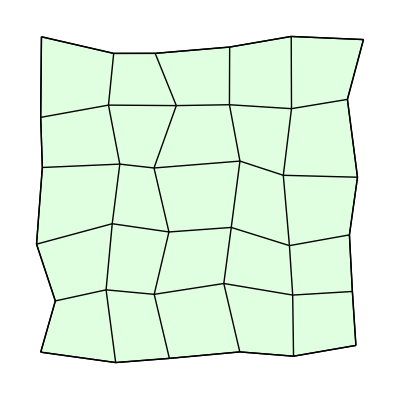

```mathematica
ShowTissue[T]
```

The tissue object has a list of vertics, followed by a list of edges, followed by a list of cells as edge numbers.

```mathematica
T
```

Tissue[{{-5.10355,-4.88676},{-2.68103,-5.22312},{-0.946039,-5.08793},{1.32967,-4.87832},{3.06585,-5.01733},{5.08146,-4.66825},{-4.63125,-3.22744},{-2.99106,-2.86814},{-1.43633,-3.01399},{0.81254,-2.6629},{3.03896,-3.03772},{4.96725,-2.92139},{-5.23846,-1.38898},{-2.79283,-0.726708},{-0.960148,-0.993885},{1.05327,-0.84722},{2.93348,-1.43634},{4.872,-1.08842},{-5.05093,1.09448},{-2.54797,1.20359},{-1.44255,1.07813},{1.33447,1.30163},{2.73537,0.841442},{5.13323,0.779222},{-5.10432,2.71697},{-2.91402,3.11458},{-0.721842,3.09859},{0.994728,3.12659},{3.00022,2.99949},{4.80685,3.29974},{-5.07978,5.32746},{-2.74531,4.78928},{-1.4048,4.79086},{1.00212,4.99468},{2.99094,5.33826},{5.32554,5.23699}},{{1,2},{1,7},{2,3},{2,8},{3,4},{3,9},{4,5},{4,10},{5,6},{5,11},{6,12},{7,8},{7,13},{8,9},{8,14},{9,10},{9,15},{10,11},{10,16},{11,12},{11,17},{12,18},{13,14},{13,19},{14,15},{14,20},{15,16},{15,21},{16,17},{16,22},{17,18},{17,23},{18,24},{19,20},{19,25},{20,21},{20,26},{21,22},{21,27},{22,23},{22,28},{23,24},{23,29},{24,30},{25,26},{25,31},{26,27},{26,32},{27,28},{27,33},{28,29},{28,34},{29,30},{29,35},{30,36},{31,32},{32,33},{33,34},{34,35},{35,36}},{{1,4,12,2},{3,6,14,4},{5,8,16,6},{7,10,18,8},{9,11,20,10},{12,15,23,13},{14,17,25,15},{16,19,27,17},{18,21,29,19},{20,22,31,21},{23,26,34,24},{25,28,36,26},{27,30,38,28},{29,32,40,30},{31,33,42,32},{34,37,45,35},{36,39,47,37},{38,41,49,39},{40,43,51,41},{42,44,53,43},{45,48,56,46},{47,50,57,48},{49,52,58,50},{51,54,59,52},{53,55,60,54}}]

### Convert to a FlatTissue

The flat tissue only has vertices and cells as vertex numbers

```mathematica
F=Tissue2FlatTissue[T]
```

FlatTissue[{{-5.10355,-4.88676},{-2.68103,-5.22312},{-0.946039,-5.08793},{1.32967,-4.87832},{3.06585,-5.01733},{5.08146,-4.66825},{-4.63125,-3.22744},{-2.99106,-2.86814},{-1.43633,-3.01399},{0.81254,-2.6629},{3.03896,-3.03772},{4.96725,-2.92139},{-5.23846,-1.38898},{-2.79283,-0.726708},{-0.960148,-0.993885},{1.05327,-0.84722},{2.93348,-1.43634},{4.872,-1.08842},{-5.05093,1.09448},{-2.54797,1.20359},{-1.44255,1.07813},{1.33447,1.30163},{2.73537,0.841442},{5.13323,0.779222},{-5.10432,2.71697},{-2.91402,3.11458},{-0.721842,3.09859},{0.994728,3.12659},{3.00022,2.99949},{4.80685,3.29974},{-5.07978,5.32746},{-2.74531,4.78928},{-1.4048,4.79086},{1.00212,4.99468},{2.99094,5.33826},{5.32554,5.23699}},{{1,2,8,7},{2,3,9,8},{3,4,10,9},{4,5,11,10},{5,6,12,11},{7,8,14,13},{8,9,15,14},{9,10,16,15},{10,11,17,16},{11,12,18,17},{13,14,20,19},{14,15,21,20},{15,16,22,21},{16,17,23,22},{17,18,24,23},{19,20,26,25},{20,21,27,26},{21,22,28,27},{22,23,29,28},{23,24,30,29},{25,26,32,31},{26,27,33,32},{27,28,34,33},{28,29,35,34},{29,30,36,35}}]

Compare the cells in the FlatTissue with the Vertex Numbers in the original tissue

```mathematica
F[[2]]
```

{{1,2,8,7},{2,3,9,8},{3,4,10,9},{4,5,11,10},{5,6,12,11},{7,8,14,13},{8,9,15,14},{9,10,16,15},{10,11,17,16},{11,12,18,17},{13,14,20,19},{14,15,21,20},{15,16,22,21},{16,17,23,22},{17,18,24,23},{19,20,26,25},{20,21,27,26},{21,22,28,27},{22,23,29,28},{23,24,30,29},{25,26,32,31},{26,27,33,32},{27,28,34,33},{28,29,35,34},{29,30,36,35}}

```mathematica
CellVertexNumbers[T]
```

{{1,2,8,7},{2,3,9,8},{3,4,10,9},{4,5,11,10},{5,6,12,11},{7,8,14,13},{8,9,15,14},{9,10,16,15},{10,11,17,16},{11,12,18,17},{13,14,20,19},{14,15,21,20},{15,16,22,21},{16,17,23,22},{17,18,24,23},{19,20,26,25},{20,21,27,26},{21,22,28,27},{22,23,29,28},{23,24,30,29},{25,26,32,31},{26,27,33,32},{27,28,34,33},{28,29,35,34},{29,30,36,35}}

### Convert the flat tissue back to the original and compare

```mathematica
Q=FlatTissue2Tissue[F];
```

```mathematica
Q==T
```

True